# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"clean"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
listDims={{100,100}(*,{150,300},{200,200},{500,300},{500,200}*)}
ims=Table[
nx=dims[[1]]/r;
ny=dims[[2]]/r;


{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io};
Print[MinMax[Flatten[ImageData[idd]]]];
{iaa,ibb,idd}
,{dims,listDims}]

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{{100,100}}

{2.17754,38.6009}

{{-Graphics-,-Graphics-,-Graphics-}}

max dv=38.6009

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,45}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,45}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Design

For a synthetical displacement of 0.5:
 
•	Initial values range: {{0,1},{-1,1},{-1,0},{-2,2}}
•	Selection criteria:
	•	We filter direction (positive solutions only)
	•	Range {0, 1} 
	•	No errors allowed
•	Magnitude threshold for gradient is e=0.0001

(* Criterias to select a solution *)

newValCon=Select[tableNewVals,(#[[3]]==”converged”&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValAny=Select[tableNewVals,((#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&&#[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValOk=Select[tableNewVals,((#[[3]]==”ok”||#[[3]]==”oksign”||#[[3]]==”okmag”)&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
noFakeConverge=Select[tableNewVals,(#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&,1];

### Test Run

```mathematica
Print["minmax dv=",MinMax[Flatten[ImageData[id]]]]
```

minmax dv={0.136895,38.6009}

```mathematica
(* Test values *)
levels={1,1};
e=0.0001;
n=0;
u=0;
steps=0.5;
v0ranges={{-30,-15},{-40,-15},{-40,-20},{-50,-20}};
```

```mathematica
(* Creating condition *)
topbot={-50,-20};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
v0Table=Table[

(* Creating list of initial Values *)
range=v0range;
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Norm[{#[[1]],#[[2]]}]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-100];
ListPlot[listv0];

bigTest[steps,n,u,listv0,condition,e,{levels},ims]

,{v0range,v0ranges}];
```

```mathematica
Print["levelTable Dimensions=",Dimensions[v0Table]]
```

levelTable Dimensions={4,1,1,4}

### More numbers

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

solution=ImageData[-ims[[1,3]]];

density=(Length[Flatten[DeleteDuplicates[#]&/@Floor[v0Table[[which,1,1,1,All,All,1]]]]])/(103.*45.);

vals=Table[
ps=Select[v0Table[[which,1,1,1,y,All,All]],1<Round[#[[1]]]<103&];
(ps[[All,2]]-solution[[y,Round[ps[[All,1]]]]])^2

,{y,Length[v0Table[[which,1,1,1]]]}];

rmse=Sqrt[Mean[Flatten[vals]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density}

,{which,Length[v0Table]}]
```

{{RMSE= ,26.1826,Density= ,0.22891},{RMSE= ,30.3473,Density= ,0.258468},{RMSE= ,30.8618,Density= ,0.200863},{RMSE= ,32.1132,Density= ,0.197195}}

### Images

```mathematica
imagesTable=Table[

solution=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[1,3]],scale,{0,1}]]}]];

images=ConformImages[Rasterize[Image[#],ImageResolution->300]&/@Flatten[{ims[[1,1;;2]],v0Table[[which,1,1,4]],solution}],{500}];

Grid[{images,numbersTable[[which]]}]

,{which,Length[v0Table]}];
```

```mathematica
imFinal=Legended[
Labeled[
Grid[Flatten[{imagesTable},{{2},{1}}]],
Column[{
Style[Row[{"Criteria range= ",topbot}],FontSize->fontsize,FontFamily->"Times",Italic],Style[Row[{"Steps= ",steps}],FontSize->fontsize,FontFamily->"Times",Italic]
},Alignment->Center],
Top],
legendBar]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 26.1826 | Density=  | 0.22891
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 30.3473 | Density=  | 0.258468
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 30.8618 | Density=  | 0.200863
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 32.1132 | Density=  | 0.197195Criteria range= {-50,-20}
Steps= 0.5

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],imFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\sintel-bamboo-clean-largemov-im.pdf

### Text

It's important to separate big displacements  from small displacements, because a non uniform behavior in the scene will lead to incongruency to our model, which is applied with the assumption that the nearest solution to the initial value, it's the right solution. This upsets variation in movement, because not every zone will profit of the same initial value.

Also, when plenty of details in the image, it’s best to address small movements first.

### More in depth

```mathematica
lvl=5;
```

```mathematica
k=1;
{ka,kb}=ImageData[#][[k]]&/@ims[[1,1;;2]];
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
(* Creating list of initial Values *)
range={-30,-15};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Norm[{#[[1]],#[[2]]}]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-100];
ListPlot[listv0];
```

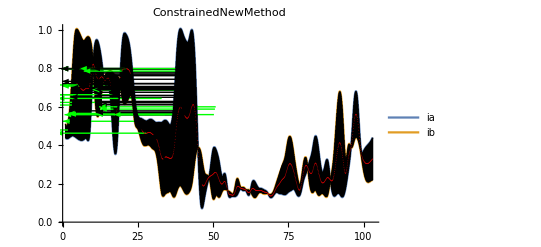

```mathematica
seeAllLine[0,0,listv0,condition,Range[1,103,0.1],pyrab[[1;;5]],e,"ConstrainedNewMethod"]
```

```mathematica
lineTest[0,u,listv0,condition,Range[1,130],pyrab[[1;;1]],e,"ConstrainedNewMethod"];
```